```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\Desktop

```mathematica
cen={2.5,7.5,15,25,35,50,70};
mub={399.8,395.6,391.6,382.4,376.1,357.8,337.8};
data=Transpose[{cen,mub}];
para1=a x+b/.FindFit[data,a x+b,{a,b},x];
fun1[x_]=para1;
para2=c x^2+a x+b/.FindFit[data,c x^2+a x+b,{a,b,c},x];
fun2[x_]=para2;
```

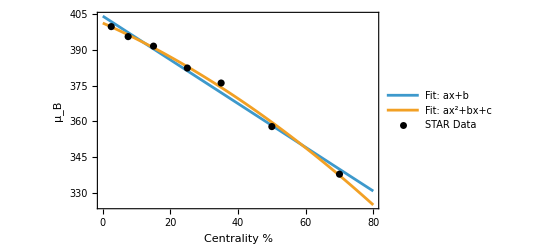

```mathematica
Show[Plot[{fun1[x],fun2[x]},{x,0,80},PlotLegends->{"Fit: ax+b","Fit: ax^2+bx+c"}],ListPlot[data,PlotStyle->Black,PlotLegends->{"STAR Data"}],Frame->True,FrameLabel->{Style["Centrality %",Black],Style["μ_B",Black],Style["√s_NN=7.7 GeV",Black]}]
```

```mathematica
cennew={0,1,2,3,4,5,6,7,8,9,10,12.5,15,17.5,20,22.5,25,27.5,30,32.5,35,37.5,40,42.5,45,47.5,50,55,60,65,70,75,80};
mubnew=fun2[cennew]
```

{401.293,400.658,400.015,399.365,398.706,398.039,397.364,396.68,395.989,395.289,394.582,392.777,390.922,389.016,387.06,385.052,382.994,380.885,378.726,376.516,374.255,371.943,369.581,367.168,364.704,362.19,359.624,354.342,348.857,343.168,337.277,331.184,324.887}